```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd CG V3 Parallel.wl"]
```

```mathematica
data=Import["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\SU4Gates9Qubits.csv"];
```

```mathematica
distloc[q1_, q2_] := 
			Norm[RydDev[AtomLocations][q1] - RydDev[AtomLocations][q2], 2] RydDev[UnitLattice];

blockadecheck[q_List] := 
			And @@ ((distloc @@ # <= (RydDev[BlockadeRadius]+$MachineEpsilon))& /@ Subsets[Flatten[q], {2}]);
```

```mathematica
(*VQD Initialisation*)locations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{2,0,0},{2,1,0},{3,0,0},{3,1,0},{4,0,0}}}];
InitParams={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 1.1
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 0
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
Options[RydbergHub]=InitParams;
RydDev=RydbergHub[];
PlotAtoms[RydDev]
```

-Graphics3D-

```mathematica
InsertCircuitNoise[{Subscript[SWAPLoc, 0,1]},RydDev]
ExtractCircuit[%]
PlotAtoms[RydDev]
InsertCircuitNoise[{Subscript[SWAPLoc, 3,6]},RydDev]
PlotAtoms[RydDev]
Options[RydbergHub]=InitParams;
RydDev=RydbergHub[];
PlotAtoms[RydDev]
```

{{0,{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}

-Graphics3D-

{{0,{Depol_3[0.],Deph_3[0.],Depol_6[0.],Deph_6[0.]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

-Graphics3D-

-Graphics3D-

```mathematica
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
```

```mathematica
SU4GateARPMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

```mathematica
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, ARP CZ*)
SU4GateDCARP[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCARP], a[[1]],a[[2]]],Subscript[CZARP, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, GA CZ*)

SU4GateDCPI[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCPI], a[[1]],a[[2]]],Subscript[CZPI, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
```

```mathematica
(*Look-up table for current grid positions of a qubit state, indexed by qubit label*)
LocTrack[Nq_]:=Range[0,Nq-1]


(*Randomly generated list, each 2 qubits represent a randomly generated pair*)
QList={0,3,2,7,1,5,6,4,8};

(*Constructed list which replaces the qubit labels with their respective current grid position labels*)
QLoclist=Table[LocTrack[Length[QList]][[QList[[i]]+1]],{i,1,Length[QList]}]

(*Sort the qubit pairs in such a way that the pairs which require the least operations to connect are first in the schedule*)
(*RTN: Pair #, Seperation between qubits as indicator of how many operations needed to connect*)
GateOrdering=SortBy[Table[{i-Quotient[i,2],Abs[QLoclist[[i]]-QLoclist[[i+1]]]},{i,1,Length[QLoclist]-1,2}],Last][[All,1]]
RQSOrd=Flatten[Table[QList[[{2*GateOrdering[[i]]-1,2*GateOrdering[[i]]}]],{i,1,Length[GateOrdering]}]]
```

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPSchedulePI[GateData_,A_,B_,LocTrackerPI_]:=Module[
{},
LocTracker=LocTrackerPI;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCPIRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPScheduleARP[GateData_,A_,B_,LocTrackerARP_]:=Module[
{},
LocTracker=LocTrackerARP;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCARPRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Generate a list of random permutations of NQ qubits*)
(*As all neutral atom qubits are fundamentally identical, we can trivially label them after the circuit has been generated, meaning we can always define the pairings for the first SU(4) layer. *)
NRandQbits[NQ_,i_]:=If[i==0,Range[0,NQ-1],RandomSample[Range[0,NQ-1],NQ]]
```

```mathematica
LocTrackerARP=LocTrack[2];
QVLayerARPPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerARP=LocTracker ;Table[
QLoclist=Table[LocTrackerARP[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPScheduleARP[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerARP];
LocTrackerARP=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]

QVLayerPIPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerPI=LocTracker ;Table[
QLoclist=Table[LocTrackerPI[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPSchedulePI[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerPI];
LocTrackerPI=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]
```

```mathematica
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Flatten[Which[StringContainsQ[ConnectivityRule,"ARPA2A"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPSWAP"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPSWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIA2A"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PISWAP"],
Table[RQS=NRandQbits[NQ,i];QVLayerPISWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIParMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPParMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"PIPropSWAP"],
Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];LocNCirc=QVLayerPIPropSWAP[DataSet,NQ,RQS,i,LocTrac];LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"ARPPropSWAP"],
Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];LocNCirc=QVLayerARPPropSWAP[DataSet,NQ,RQS,i,LocTrac];LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}]
],1]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
(*Print[Circ1];*)
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
Print[DrawCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]
```

-Graphics3D-

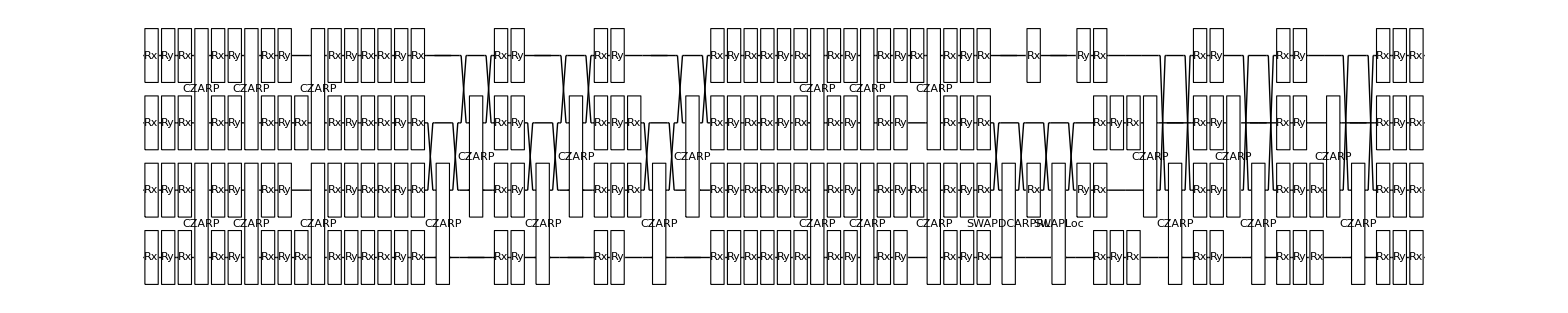

```mathematica
Options[RydbergHub]=InitParams;
RydDev=RydbergHub[];
PlotAtoms[RydDev]
TestCirc=QVCirc[data[[1;;36]],4,"ARPPropSWAP"];
ExtractCircuit[GetCircuitSchedule[TestCirc,RydDev]];
DrawCircuit[%]
(*DrawCircuit[%]
InsertCircuitNoise[TestCirc,RydDev]*)
(*Table[
InsertCircuitNoise[TestCirc[[i]],RydDev];
Print[i];
Print[TestCirc[[i]]];
Print[DrawCircuit[TestCirc[[i]]]];
Print[PlotAtoms[RydDev]],{i,1,Length[TestCirc]}]*)
(*SWAPSchedulePI[data[[1]],0,1,{0,1}]*)
```

```mathematica
Options[RydbergHub]=InitParams;
RydDev=RydbergHub[];
```

```mathematica
TC1={Subscript[SWAPDCARPRL, 2,0],Subscript[SWAPLoc, 2,0],Subscript[Rx, 2][-1.1212731104749931],Subscript[Ry, 2][1.2299244543393544],Subscript[Rx, 2][2.8077509123491007],Subscript[Rx, 1][1.6986283009881102],Subscript[Ry, 1][2.1154322575416695],Subscript[Rx, 1][0.7729219120566526],Subscript[CZARP, 2,1],Subscript[Rx, 2][2.142459364717361],Subscript[Ry, 2][3.141592653589793],Subscript[Rx, 1][0.06965313073311563],Subscript[Ry, 1][-1.5707963267948968],Subscript[CZARP, 2,1],Subscript[Rx, 2][1.446881103948436],Subscript[Ry, 2][1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966],Subscript[Rx, 1][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[CZARP, 2,1],Subscript[Rx, 2][-1.1353992004089921],Subscript[Ry, 2][0.6989390697846843],Subscript[Rx, 2][-2.1604610195490777],Subscript[Rx, 1][2.6994775135733775],Subscript[Ry, 1][0.9296751031009444],Subscript[Rx, 1][0.44676065524345976]};
InsertCircuitNoise[TC1,RydDev];
PlotAtoms[RydDev]
```

-Graphics3D-

```mathematica
PlotAtoms[RydDev]
TC2={{Subscript[SWAPDCARPRL, 3,1],Subscript[SWAPLoc, 3,1]},{Subscript[Rx, 0][-2.069448446955011],Subscript[Ry, 0][0.6144880335979012],Subscript[Rx, 0][-0.6998692115229868],Subscript[Rx, 3][2.3533529958515054],Subscript[Ry, 3][0.6536893633606041],Subscript[Rx, 3][1.6734588044758816],Subscript[CZARP, 0,3],Subscript[Rx, 0][2.017368794962991],Subscript[Ry, 0][3.141592653589793],Subscript[Rx, 3][0.11491372893429386],Subscript[Ry, 3][-1.5707963267948966],Subscript[CZARP, 0,3],Subscript[Rx, 0][1.3512677308239045],Subscript[Ry, 0][1.570796326794897],Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 3][1.5707963267948966],Subscript[Ry, 3][1.5707963267948966],Subscript[CZARP, 0,3],Subscript[Rx, 0][-0.7059011700466171],Subscript[Ry, 0][2.0519607506303608],Subscript[Rx, 0][-1.1305279054485098],Subscript[Rx, 3][0.5469100601085137],Subscript[Ry, 3][1.4422897723395034],Subscript[Rx, 3][-0.8177592740480772]}};
InsertCircuitNoise[TC2,RydDev];
PlotAtoms[RydDev]
```

-Graphics3D-

InsertCircuitNoise::error: Encountered gate CZARP_(0,3) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

-Graphics3D-

```mathematica
TC3={Subscript[Rx, 3][-2.069448446955011],Subscript[Ry, 3][0.6144880335979012],Subscript[Rx, 3][-0.6998692115229868],Subscript[Rx, 0][2.3533529958515054],Subscript[Ry, 0][0.6536893633606041],Subscript[Rx, 0][1.6734588044758816],Subscript[CZARP, 3,0],Subscript[Rx, 3][2.017368794962991],Subscript[Ry, 3][3.141592653589793],Subscript[Rx, 0][0.11491372893429386],Subscript[Ry, 0][-1.5707963267948966],Subscript[CZARP, 3,0],Subscript[Rx, 3][1.3512677308239045],Subscript[Ry, 3][1.570796326794897],Subscript[Rx, 3][-1.5707963267948966],Subscript[Rx, 0][1.5707963267948966],Subscript[Ry, 0][1.5707963267948966],Subscript[CZARP, 3,0],Subscript[Rx, 3][-0.7059011700466171],Subscript[Ry, 3][2.0519607506303608],Subscript[Rx, 3][-1.1305279054485098],Subscript[Rx, 0][0.5469100601085137],Subscript[Ry, 0][1.4422897723395034],Subscript[Rx, 0][-0.8177592740480772]}
```

-Graphics3D-

-Graphics3D-

{{0,{H_0,Deph_0[1.67785×10^-7],UNonNorm_(0,2)[{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}],H_0,Deph_0[1.67785×10^-7],H_2,Deph_0[1.67785×10^-7],UNonNorm_(2,0)[{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}],H_2,Deph_2[1.67785×10^-7],H_0,Deph_0[1.67785×10^-7],UNonNorm_(0,2)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],H_0,Deph_0[1.67785×10^-7],SWAP_(0,2)},{Deph_0[0.],Deph_1[5.5256×10^-6],Deph_2[0.],Deph_3[5.5256×10^-6],Deph_4[5.5256×10^-6],Deph_5[5.5256×10^-6],Deph_6[5.5256×10^-6],Deph_7[5.5256×10^-6],Deph_8[5.5256×10^-6]}},{16.4664,{Depol_0[0.],Deph_0[0.],Depol_2[0.],Deph_2[0.]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{16.4664,{},{}}}

{}

-Graphics3D-

{{0,{Depol_0[0.],Deph_0[0.],Depol_2[0.],Deph_2[0.]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

-Graphics3D-

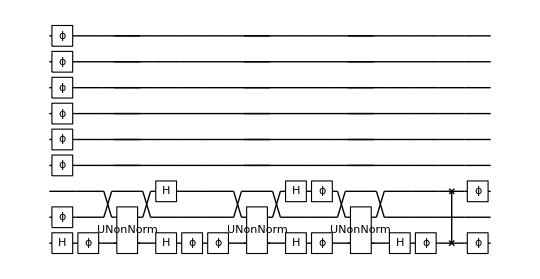

-Graphics3D-

InsertCircuitNoise::error: Encountered gate SWAPDCARPRL_(0,2) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

```mathematica
Options[RydbergHub]=InitParams;
RydDev=RydbergHub[];
PlotAtoms[RydDev]
InsertCircuitNoise[{Subscript[SWAPDCARPRL, 0,2],Subscript[SWAPLoc, 0,2]},RydDev]
GetUnsupportedGates[{Subscript[SWAPDCARPRL, 0,2],Subscript[SWAPLoc, 0,2]},RydDev]
PlotAtoms[RydDev]
InsertCircuitNoise[{Subscript[SWAPLoc, 0,2]},RydDev]
PlotAtoms[RydDev]
DrawCircuit[ExtractCircuit[InsertCircuitNoise[{Subscript[SWAPDCARPRL, 0,2]},RydDev,ReplaceAliases->True]]]
```

```mathematica
?GetUnsupportedGates
```

```mathematica
Flatten[Position[{1,2,0,3},{1,2,0,3}⟦3+1⟧-2]]⟦1⟧
SAD={1,2,0,3}
(SAD⟦Flatten[Position[{1,2,0,3},{1,2,0,3}⟦3+1⟧-2]]⟦1⟧⟧)+=1
SAD
```

1

{1,2,0,3}

2

{2,2,0,3}

```mathematica
QVLayerARPSWAP[data,2,{0,1},0,LocTrackerARP]
```

{0,1}

{0,1}

1

Yup

Aligned

{{{Rx_0[-1.39898],Ry_0[1.62867],Rx_0[1.45827],Rx_1[2.35008],Ry_1[0.941758],Rx_1[-0.467045],CZARP_(0,1),Rx_0[1.96106],Ry_0[3.14159],Rx_1[0.231888],Ry_1[-1.5708],CZARP_(0,1),Rx_0[1.81862],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZARP_(0,1),Rx_0[1.13586],Ry_0[1.30701],Rx_0[-0.417784],Rx_1[-1.30951],Ry_1[1.57267],Rx_1[2.88766]}}}

{}

```mathematica
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Which[StringContainsQ[ConnectivityRule,"ARPA2A"],
Table[RQS=NRandQbits[NQ];QVLayerARPA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPSWAP"],
Table[RQS=NRandQbits[NQ];QVLayerARPSWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIA2A"],
Table[RQS=NRandQbits[NQ];QVLayerPIA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PISWAP"],
Table[RQS=NRandQbits[NQ];QVLayerPISWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIParMove"],
Table[RQS=NRandQbits[NQ];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPParMove"],
Table[RQS=NRandQbits[NQ];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}]
]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
(*Perfect renormalisation on a given circuit, unsure if this is best or if taking an average across the NCirc is a more "accurate" scheme*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
Initialisation={InitCirc[Reg,MaxNQ]};
InitCircuit=Join[Initialisation,Circ1];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];
```

{Rx_0[π],Rx_1[π],CZARP_(0,1),Rx_1[π]}

```mathematica
NQ=5
RQs={0,1,2,3,4}
ARPCZdur=1
(*Parallelised SU4 Gate layer generators*)
SU4GateARPParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GatePIParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPIPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

MoveTime=300
QVLayerARPParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GateARPParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SpareARP, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]
QVLayerPIParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GatePIParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SparePI, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]
```

{{Rx_0[1.79004],Rx_1[1.88613],Rx_2[-1.80032],Rx_3[2.3115]},{Ry_0[1.46704],Ry_1[2.55694],Ry_2[1.27185],Ry_3[1.57278]},{Rx_0[-2.48457],Rx_1[2.50974],Rx_2[-1.00828],Rx_3[-1.23637]},{CZPIPar_(0,1),CZPIPar_(2,3),SparePI_4,Wait_0[300]},{Rx_0[2.21178],Rx_1[0.377692],Rx_2[2.18388],Rx_3[0.0804764]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZPIPar_(0,1),CZPIPar_(2,3),SparePI_4,Wait_0[300]},{Rx_0[1.21967],Rx_1[1.5708],Rx_2[1.83928],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZPIPar_(0,1),CZPIPar_(2,3),SparePI_4,Wait_0[300]},{Rx_0[1.67234],Rx_1[0.637274],Rx_2[-1.96605],Rx_3[-2.48805]},{Ry_0[0.753038],Ry_1[2.31189],Ry_2[1.70085],Ry_3[2.48581]},{Rx_0[-2.65359],Rx_1[-2.1245],Rx_2[-2.55203],Rx_3[2.14997]}}

{{0,{Rx_0[1.79004],Deph_0[9.56017×10^-8],Rx_1[1.88613],Deph_1[1.00734×10^-7],Rx_2[-1.80032],Deph_2[9.61507×10^-8],Rx_3[2.3115],Deph_3[1.23452×10^-7]},{Deph_0[1.74988×10^-7],Deph_1[1.42743×10^-7],Deph_2[1.71539×10^-7],Deph_3[0.],Deph_4[7.75671×10^-7],Deph_5[7.75671×10^-7],Deph_6[7.75671×10^-7],Deph_7[7.75671×10^-7],Deph_8[7.75671×10^-7]}},{2.3115,{Ry_0[1.46704],Deph_0[7.83514×10^-8],Ry_1[2.55694],Deph_1[1.3656×10^-7],Ry_2[1.27185],Deph_2[6.79267×10^-8],Ry_3[1.57278],Deph_3[8.39984×10^-8]},{Deph_0[3.65738×10^-7],Deph_1[0.],Deph_2[4.31238×10^-7],Deph_3[3.30257×10^-7],Deph_4[8.58034×10^-7],Deph_5[8.58034×10^-7],Deph_6[8.58034×10^-7],Deph_7[8.58034×10^-7],Deph_8[8.58034×10^-7]}},{4.86844,{Rx_0[-2.48457],Deph_0[1.32695×10^-7],Rx_1[2.50974],Deph_1[1.34039×10^-7],Rx_2[-1.00828],Deph_2[5.38501×10^-8],Rx_3[-1.23637],Deph_3[6.60316×10^-8]},{Deph_0[8.44605×10^-9],Deph_1[0.],Deph_2[5.03844×10^-7],Deph_3[4.27306×10^-7],Deph_4[8.42194×10^-7],Deph_5[8.42194×10^-7],Deph_6[8.42194×10^-7],Deph_7[8.42194×10^-7],Deph_8[8.42194×10^-7]}},{7.37818,{UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],UNonNorm_(2,3)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],Deph_4[1.00671×10^-7],Deph_0[0.000100661]},{Deph_0[0.],Deph_1[0.000100661],Deph_2[0.000100661],Deph_3[0.000100661],Deph_4[0.000100661],Deph_5[0.000100661],Deph_6[0.000100661],Deph_7[0.000100661],Deph_8[0.000100661]}},{307.378,{Rx_0[2.21178],Deph_0[1.18126×10^-7],Rx_1[0.377692],Deph_1[2.01717×10^-8],Rx_2[2.18388],Deph_2[1.16636×10^-7],Rx_3[0.0804764],Deph_3[4.29806×10^-9]},{Deph_0[0.],Deph_1[6.15464×10^-7],Deph_2[9.36291×10^-9],Deph_3[7.15201×10^-7],Deph_4[7.42206×10^-7],Deph_5[7.42206×10^-7],Deph_6[7.42206×10^-7],Deph_7[7.42206×10^-7],Deph_8[7.42206×10^-7]}},{309.59,{Ry_0[3.14159],Deph_0[1.67785×10^-7],Ry_1[-1.5708],Deph_1[8.38926×10^-8],Ry_2[3.14159],Deph_2[1.67785×10^-7],Ry_3[-1.5708],Deph_3[8.38926×10^-8]},{Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}},{312.732,{UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],UNonNorm_(2,3)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],Deph_4[1.00671×10^-7],Deph_0[0.000100661]},{Deph_0[0.],Deph_1[0.000100661],Deph_2[0.000100661],Deph_3[0.000100661],Deph_4[0.000100661],Deph_5[0.000100661],Deph_6[0.000100661],Deph_7[0.000100661],Deph_8[0.000100661]}},{612.732,{Rx_0[1.21967],Deph_0[6.51397×10^-8],Rx_1[1.5708],Deph_1[8.38926×10^-8],Rx_2[1.83928],Deph_2[9.82319×10^-8],Rx_3[1.5708],Deph_3[8.38926×10^-8]},{Deph_0[2.07924×10^-7],Deph_1[9.00961×10^-8],Deph_2[0.],Deph_3[9.00961×10^-8],Deph_4[6.17209×10^-7],Deph_5[6.17209×10^-7],Deph_6[6.17209×10^-7],Deph_7[6.17209×10^-7],Deph_8[6.17209×10^-7]}},{614.571,{Ry_0[1.5708],Deph_0[8.38926×10^-8],Ry_1[1.5708],Deph_1[8.38926×10^-8],Ry_2[1.5708],Deph_2[8.38926×10^-8],Ry_3[1.5708],Deph_3[8.38926×10^-8]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7]}},{616.142,{Rx_0[-1.5708],Deph_0[8.38926×10^-8],Rx_2[-1.5708],Deph_2[8.38926×10^-8]},{Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7]}},{617.712,{UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],UNonNorm_(2,3)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],Deph_4[1.00671×10^-7],Deph_0[0.000100661]},{Deph_0[0.],Deph_1[0.000100661],Deph_2[0.000100661],Deph_3[0.000100661],Deph_4[0.000100661],Deph_5[0.000100661],Deph_6[0.000100661],Deph_7[0.000100661],Deph_8[0.000100661]}},{917.712,{Rx_0[1.67234],Deph_0[8.93157×10^-8],Rx_1[0.637274],Deph_1[3.40354×10^-8],Rx_2[-1.96605],Deph_2[1.05002×10^-7],Rx_3[-2.48805],Deph_3[1.32881×10^-7]},{Deph_0[2.73729×10^-7],Deph_1[6.21066×10^-7],Deph_2[1.75168×10^-7],Deph_3[0.],Deph_4[8.34916×10^-7],Deph_5[8.34916×10^-7],Deph_6[8.34916×10^-7],Deph_7[8.34916×10^-7],Deph_8[8.34916×10^-7]}},{920.2,{Ry_0[0.753038],Deph_0[4.0218×10^-8],Ry_1[2.31189],Deph_1[1.23473×10^-7],Ry_2[1.70085],Deph_2[9.08383×10^-8],Ry_3[2.48581],Deph_3[1.32761×10^-7]},{Deph_0[5.81467×10^-7],Deph_1[5.83615×10^-8],Deph_2[2.6341×10^-7],Deph_3[0.],Deph_4[8.34164×10^-7],Deph_5[8.34164×10^-7],Deph_6[8.34164×10^-7],Deph_7[8.34164×10^-7],Deph_8[8.34164×10^-7]}},{922.686,{Rx_0[-2.65359],Deph_0[1.41722×10^-7],Rx_1[-2.1245],Deph_1[1.13465×10^-7],Rx_2[-2.55203],Deph_2[1.36298×10^-7],Rx_3[2.14997],Deph_3[1.14825×10^-7]},{Deph_0[0.],Deph_1[1.77546×10^-7],Deph_2[3.40795×10^-8],Deph_3[1.68999×10^-7],Deph_4[8.90464×10^-7],Deph_5[8.90464×10^-7],Deph_6[8.90464×10^-7],Deph_7[8.90464×10^-7],Deph_8[8.90464×10^-7]}},{925.34,{},{}}}

{{0,{Rx_0[1.79004],Rx_1[1.88613],Rx_2[-1.80032],Rx_3[2.3115]}},{2.3115,{Ry_0[1.46704],Ry_1[2.55694],Ry_2[1.27185],Ry_3[1.57278]}},{4.86844,{Rx_0[-2.48457],Rx_1[2.50974],Rx_2[-1.00828],Rx_3[-1.23637]}},{7.37818,{U_(0,1)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],U_(2,3)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Id_4}},{307.378,{Rx_0[2.21178],Rx_1[0.377692],Rx_2[2.18388],Rx_3[0.0804764]}},{309.59,{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]}},{312.732,{U_(0,1)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],U_(2,3)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Id_4}},{612.732,{Rx_0[1.21967],Rx_1[1.5708],Rx_2[1.83928],Rx_3[1.5708]}},{614.571,{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]}},{616.142,{Rx_0[-1.5708],Rx_2[-1.5708]}},{617.712,{U_(0,1)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],U_(2,3)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Id_4}},{917.712,{Rx_0[1.67234],Rx_1[0.637274],Rx_2[-1.96605],Rx_3[-2.48805]}},{920.2,{Ry_0[0.753038],Ry_1[2.31189],Ry_2[1.70085],Ry_3[2.48581]}},{922.686,{Rx_0[-2.65359],Rx_1[-2.1245],Rx_2[-2.55203],Rx_3[2.14997]}},{925.34,{}}}

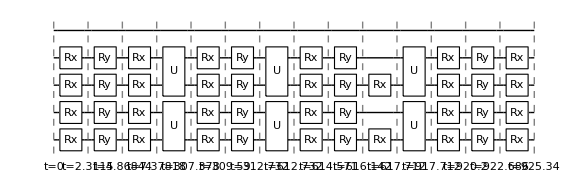

{}

```mathematica
ParallelLayer=QVLayerPIParMove[{data[[200]],data[[1000]]},5,{0,1,2,3,4},0]
TestRho=CreateDensityQureg[9];
InitZeroState[TestRho];
NoisyCirc=InsertCircuitNoise[ParallelLayer,RydDev,ReplaceAliases->True]
ParCircSched=GetCircuitSchedule[ParallelLayer,RydDev,ReplaceAliases->True]
DrawCircuit[%]
ApplyCircuit[TestRho,ExtractCircuit[ParCircSched]]
```

{{Rx_0[1.79004],Rx_1[1.88613],Rx_2[-1.80032],Rx_3[2.3115]},{Ry_0[1.46704],Ry_1[2.55694],Ry_2[1.27185],Ry_3[1.57278]},{Rx_0[-2.48457],Rx_1[2.50974],Rx_2[-1.00828],Rx_3[-1.23637]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[2.21178],Rx_1[0.377692],Rx_2[2.18388],Rx_3[0.0804764]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.21967],Rx_1[1.5708],Rx_2[1.83928],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.67234],Rx_1[0.637274],Rx_2[-1.96605],Rx_3[-2.48805]},{Ry_0[0.753038],Ry_1[2.31189],Ry_2[1.70085],Ry_3[2.48581]},{Rx_0[-2.65359],Rx_1[-2.1245],Rx_2[-2.55203],Rx_3[2.14997]}}

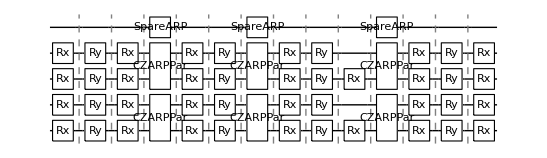

7

```mathematica
ParallelLayerOld={{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]},{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]},{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]},{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]},{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]},{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]},{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]},{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}}
DrawCircuit[%]
```

```mathematica
{{0,{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]}},{2.3115020985994335,{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]}},{4.868444580144691,{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]}},{7.378183853974558,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{7.378183853974558,{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]}},{9.589960485556027,{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]}},{12.73155313914582,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{12.73155313914582,{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]}},{14.57083595979964,{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]}},{16.141632286594536,{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]}},{17.712428613389434,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{17.712428613389434,{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]}},{20.20048116641229,{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]}},{22.686291109210224,{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}},{25.339876932834745,{}}}
```

```mathematica
InsertCircuitNoise[{Subscript[SpareARP, 0]},RydDev,ReplaceAliases->True]
```

{{0,{Deph_0[4.36241×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

5

{0,1,2,3,4}

1

General::munfl: Exp[-671141.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]},{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]},{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]},{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]},{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}}

{{0,{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]}},{2.35008,{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]}},{3.97875,{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]}},{6.44257,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{7.74257,{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]}},{9.99496,{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]}},{13.1366,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{14.4366,{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]}},{16.2552,{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]}},{17.826,{Rx_0[-1.5708],Rx_2[-1.5708]}},{19.3968,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{20.6968,{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]}},{23.7696,{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]}},{26.4959,{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}},{29.3836,{}}}

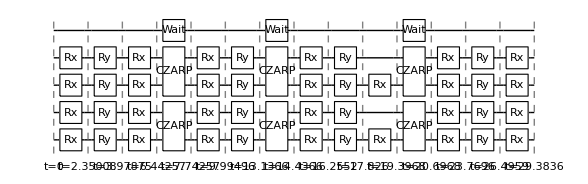

RydbergHub[T2]

```mathematica
?InsertCircuitNoise
```

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];
```

```mathematica
SU4GateARPMove[data[[1]],0,1]
SU4GateARPMove[data[[4]],0,1]
```

{{Rx_0[-1.39898],Ry_0[1.62867],Rx_0[1.45827],Rx_1[2.35008],Ry_1[0.941758],Rx_1[-0.467045]},{CZARP_(0,1)},{Rx_0[1.96106],Ry_0[3.14159],Rx_1[0.231888],Ry_1[-1.5708]},{CZARP_(0,1)},{Rx_0[1.81862],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708]},{CZARP_(0,1)},{Rx_0[1.13586],Ry_0[1.30701],Rx_0[-0.417784],Rx_1[-1.30951],Ry_1[1.57267],Rx_1[2.88766]}}

```mathematica
?Join
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?Wait
```

```mathematica
InsertCircuitNoise[CircRydbergHub[{Subscript[Wait, 0][1000]},RydDev,Parallel->True],RydDev]
```

{{0,{Deph_0[0.000335458]},{Deph_0[0.],Deph_1[0.000335458],Deph_2[0.000335458],Deph_3[0.000335458],Deph_4[0.000335458],Deph_5[0.000335458],Deph_6[0.000335458],Deph_7[0.000335458],Deph_8[0.000335458]}},{1000,{},{}}}

{{0,{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}},{π,{},{Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}}}

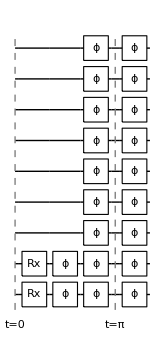

7

7

{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

$Failed

```mathematica
Tes=InsertCircuitNoise[GetCircuitSchedule[CircRydbergHub[{Subscript[Rx, 0][Pi],Subscript[Rx, 1][Pi]},RydDev,Parallel->True],RydDev],RydDev]
DrawCircuit[%]
Te=CreateDensityQureg[9]
InitZeroState[Te]
ExtractCircuit[Tes]
ApplyCircuit[Te,ExtractCircuit[Tes]]
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?ApplyCircuit
```

```mathematica
?QuEST`Gate`*
```

```mathematica
CalcCircuitMatrix[{Subscript[Id, 0]}]
```

{{1,0},{0,1}}

```mathematica
{Subscript[H, q1],Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[UNonNorm,q1,q2][{{{1,0,0,0},{0,0.9990*Exp[I*0.9906*Pi],0,0},{0,0,0.9990*Exp[I*0.9906*Pi],0},{0,0,0,0.9986*Exp[I*Pi]}}}],Subscript[H, q1],Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[H, q2],Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[UNonNorm,q2,q1][{{1,0,0,0},{0,0.9990*Exp[I*0.9906*Pi],0,0},{0,0,0.9990*Exp[I*0.9906*Pi],0},{0,0,0,0.9986*Exp[I*Pi]}}],Subscript[H, q2],Subscript[Deph, q2][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[H, q1],Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[UNonNorm,q1,q2][{{{1,0,0,0},{0,0.9990*Exp[I*0.9906*Pi],0,0},{0,0,0.9990*Exp[I*0.9906*Pi],0},{0,0,0,0.9986*Exp[I*Pi]}}}],Subscript[H, q1],
Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],Subscript[SWAP,q1,q2],Subscript[SWAPLoc,q1,q2]}
```

```mathematica
{{1,0,0,0},{0,0.999320*Exp[I*(-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0.998487-0.0408016 ⅈ | 0 | 0
0 | 0 | 0.998487-0.0408016 ⅈ | 0
0 | 0 | 0 | -0.998348+0.0470809 ⅈ)

```mathematica
0.9984867013711871-0.04080158801916461 ⅈ
```

0.998487-0.0408016 ⅈ

```mathematica
"convert to exponential"0.9984867013711871-0.04080158801916461 ⅈWith[{n=Abs[0.9984867013711871-0.04080158801916461 ⅈ],a=Arg[0.9984867013711871-0.04080158801916461 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.99932 ⅇ^(ⅈ (-0.0408407))

```mathematica
{Subscript[H, q1],
Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],
Subscript[UNonNorm,q1,q2][
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}
],
Subscript[H, q1],
Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],
Subscript[H, q2],Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],
Subscript[UNonNorm,q2,q1][
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}
],
Subscript[H, q2],
Subscript[Deph, q2][0.5 (1 - E^(-0.5 /(rabifreq t2)))],
Subscript[H, q1],
Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))],
Subscript[UNonNorm,q2,q1][
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}
],
Subscript[H, q1],
Subscript[Deph, q1][0.5 (1 - E^(-0.5 /(rabifreq t2)))]}
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}//MatrixForm
```

{H_q1,Deph_q1[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))],UNonNorm_(q1,q2)[{{1,0,0,0},{0,0.998487-0.0408016 ⅈ,0,0},{0,0,0.998487-0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],H_q1,Deph_q1[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))],H_q2,Deph_q1[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))],UNonNorm_(q2,q1)[{{1,0,0,0},{0,0.998487-0.0408016 ⅈ,0,0},{0,0,0.998487-0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],H_q2,Deph_q2[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))],H_q1,Deph_q1[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))],UNonNorm_(q2,q1)[{{1,0,0,0},{0,0.998487-0.0408016 ⅈ,0,0},{0,0,0.998487-0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}],H_q1,Deph_q1[0.5 (1-ⅇ^(-0.5/(rabifreq t2)))]}

(1 | 0 | 0 | 0
0 | 0.998487-0.0408016 ⅈ | 0 | 0
0 | 0 | 0.998487-0.0408016 ⅈ | 0
0 | 0 | 0 | -0.998348+0.0470809 ⅈ)

```mathematica
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0.998487-0.0408016 ⅈ | 0 | 0
0 | 0 | 0.998487-0.0408016 ⅈ | 0
0 | 0 | 0 | -0.998348+0.0470809 ⅈ)

```mathematica
{{1,0,0,0},{0,0.999320*Exp[I*(2-0.013)*Pi],0,0},{0,0,0.999320*Exp[I*(2-0.013)*Pi],0},{0,0,0,0.999458*Exp[I*0.985*Pi]}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0.998487-0.0408016 ⅈ | 0 | 0
0 | 0 | 0.998487-0.0408016 ⅈ | 0
0 | 0 | 0 | -0.998348+0.0470809 ⅈ)